# G1 (p=0, tau) from Σ1(p=0,iomega)

```mathematica
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/Mathematica/"];
<<params.mx;
SetDirectory["/home/h/H.Guertner/theorie/BEC_Polaron/"];
p =0;
μ = Import["DiagMC_BEC.json", {"Data", "Chemical_Potential"} ];
α= Import["DiagMC_BEC.json", {"Data", "Alpha"} ];
mr = Import["DiagMC_BEC.json", {"Data", "Impurity_Mass"} ];
qc = Import["DiagMC_BEC.json", {"Data", "Q_Cutoff"} ];
wlist = Import["DiagMC_BEC.json", {"Data", "Ws_for_Epol"} ];
```

## Integrand for q Integral

0.000137801

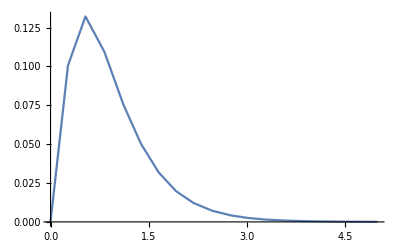

```mathematica
sew[q_, w_]:= - vq2FP[q]/(I*w-q^2/2+μ-1);
gw[q_,w_]:= ((I w+μ)-sew[q,w])^-1;
gmg0w[q_,w_]:= gw[q,w] - (I w+μ)^-1;
gmg0[t_]:= 2 * Re[NIntegrate[(4*Pi)/(2*Pi)^4 * q^2* gmg0w[q,w]*Exp[- I * w *t],{q, 0, qc}, {w, 0, 100}, AccuracyGoal->3]]
2 * Re[NIntegrate[(4*Pi)/(2*Pi)^4 * q^2* gmg0w[q,w]*Exp[- I * w*4.5],{q, 0, qc}, {w, 0, 100}, AccuracyGoal->3]]
Plot[gmg0[t], {t,0,5}, PlotPoints->10, MaxRecursion->1]
(*NIntegrate[(4*Pi)/(2*Pi)^3 * q^2* gmg0w[q,w]*Exp[- I * w],{q, 0, qc}, {w, -100, 100}]*)
```

```mathematica
data= Table[{t,gmg0[t]+g0FP[p,0,t]}, {t, 4.5, 4.7, 0.1} ]
```

$Aborted

```mathematica
Export["peter/mat_1st_g_from_se", data, "Table"];
```